```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];


vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]
maxR = 20;
maxIndex = 40;

Print["R=",vSg1Data[[maxIndex,1]], ", A=",vSg1Data[[maxIndex,4]],", p=", vSg1Data[[maxIndex,5]]];
Print["R=",vSu2Data[[maxIndex,1]], ", A=",vSu2Data[[maxIndex,4]],", p=", vSu2Data[[maxIndex,5]]];
```

maxR=31

R=27, A=5690.91, p=27.1889

R=27, A=210927., p=27.2254

0.00074606

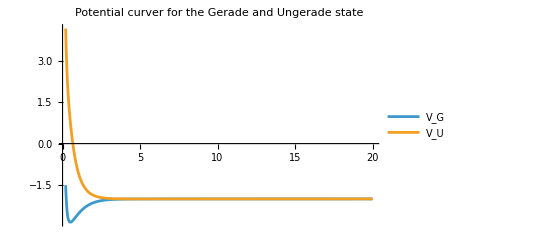

```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]
```

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{norm1, norm2,dInt, l1,l2,m1,m2,lmNorm1, lmNorm2},
(* 1s wavefunction *)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m1=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a1 + p1^2 η^2)M[η]==0, M[0.999]==0,M'[0.999]==1}, M,{η,-.999,.999}];

(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m2=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a2 + p2^2 η^2)M[η]==0, M[0.999]==0,M'[0.999]==1}, M,{η,-.999,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[ξ] m1[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[ξ]m2[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];

lmNorm1[ξ_,η_]:=1/norm1 l1[ξ]m1[η];
lmNorm2[ξ_,η_]:=1/norm2 l2[ξ]m2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[ξ,η]]ξ η lmNorm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,maxDistance}];
{R,dInt }
];

singleDR[vSg1Data[[24]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
(*singleDR[vSg1Data[[14]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[15]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],5]*)
```

R=11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.95764×10^-51 and 7.54069×10^-56 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.06331×10^-49 and 8.5819×10^-54 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0027797 and 0.000143046 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{11,0.462472}

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.2

R=0.3

R=0.4

R=0.5

R=0.6

R=0.7

R=0.8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.07219×10^-50 and 2.5711×10^-56 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

R=0.9

R=1.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

R=1.1

R=1.5

R=2.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.19349×10^-50 and 5.28136×10^-55 for the integral and error estimates.

R=2.5

R=3.

R=3.5

R=4.

R=4.5

R=5.

R=6

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93868×10^-48 and 1.69197×10^-52 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

R=7

R=8

R=9

R=10

R=11

R=12

R=13

R=14

R=15

R=16

R=17

R=18

R=19

R=20

R=21

R=22

R=23

R=24

R=25

R=26

R=27

```mathematica
allDR // MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

(0.2 | -0.960896
0.3 | 1.43123
0.4 | 0.737663
0.5 | -18.0957
0.6 | -52.7847
0.7 | -91.3167
0.8 | 0.481727
0.9 | 208.76
1. | 0.125 NIntegrate[(Conjugate[lmNorm1$13114[ξ,η]] ξ η lmNorm2$13114[ξ,η] (ξ^2-η^2))/(√(ξ^2-1) √(1-η^2)),{η,-0.999,0.999},{ξ,1.001,20}]
1.1 | -388.028
1.5 | -990.253
2. | -135.299
2.5 | -4015.67
3. | 810.209
3.5 | -696.408
4. | 10950.
4.5 | 1538.58
5. | -328.953
6 | 2232.79
7 | -13560.5
8 | -377.816
9 | -1249.92
10 | 198.706
11 | -218.472
12 | -8215.95
13 | -15011.5
14 | 11931.3
15 | 100592.
16 | 570607.
17 | -37545.9
18 | -24496.9
19 | 70889.
20 | -134235.
21 | 8149.77
22 | -1.23523×10^6
23 | 6951.54
24 | 1.53694×10^6
25 | 614896.
26 | 1.02893×10^6
27 | 838927.)

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

{{0.2,-8.14648×10^-30},{0.3,1.2134×10^-29},{0.4,6.25391×10^-30},{0.5,-1.53415×10^-28},{0.6,-4.47509×10^-28},{0.7,-7.74183×10^-28},{0.8,4.08408×10^-30},{0.9,1.76987×10^-27},{1.,1.05975×10^-30 NIntegrate[(Conjugate[lmNorm1$13114[ξ,η]] ξ η lmNorm2$13114[ξ,η] (ξ^2-η^2))/(√(ξ^2-1) √(1-η^2)),{η,-0.999,0.999},{ξ,1.001,20}]},{1.1,-3.2897×10^-27},{1.5,-8.39537×10^-27},{2.,-1.14707×10^-27},{2.5,-3.40449×10^-26},{3.,6.86895×10^-27},{3.5,-5.90414×10^-27},{4.,9.28339×10^-26},{4.5,1.30441×10^-26},{5.,-2.78887×10^-27},{6,1.89296×10^-26},{7,-1.14966×10^-25},{8,-3.20313×10^-27},{9,-1.05968×10^-26},{10,1.68463×10^-27},{11,-1.85221×10^-27},{12,-6.96549×10^-26},{13,-1.27268×10^-25},{14,1.01154×10^-25},{15,8.52822×10^-25},{16,4.83761×10^-24},{17,-3.18314×10^-25},{18,-2.07684×10^-25},{19,6.00997×10^-25},{20,-1.13804×10^-24},{21,6.90937×10^-26},{22,-1.04723×10^-23},{23,5.89352×10^-26},{24,1.30302×10^-23},{25,5.21309×10^-24},{26,8.72331×10^-24},{27,7.11243×10^-24}}

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.100141} lies outside the range of data in the interpolating function. Extrapolation will be used.

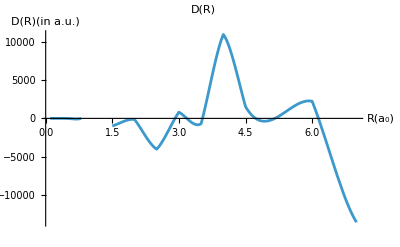

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand («1»)/(√(1-η^2) √(-1+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.100407} lies outside the range of data in the interpolating function. Extrapolation will be used.

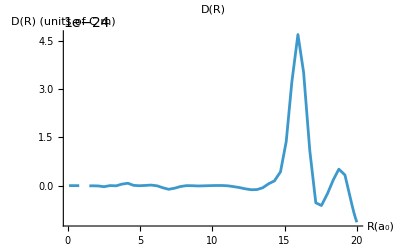

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, 7}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full, Axes->True]
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

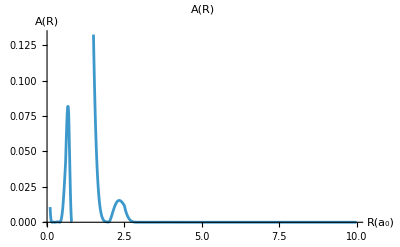

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

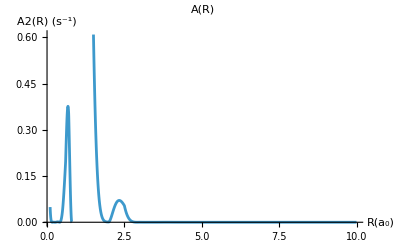

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand («1»)/(√(1.-1. η^2) √(-1.+ξ^2)) has evaluated to Overflow, Indeterminate or Infinity for all sampling points in the region with boundaries {{-0.999,0.999},{1.001,20.}}.

InterpolatingFunction::dmval: Input value {0.1001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

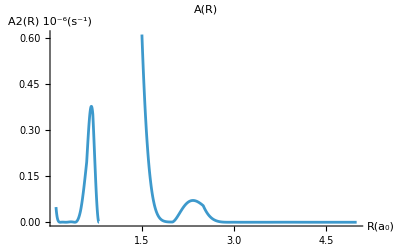

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;

aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;

aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r]*10^(-6),{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A2(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r]*10^(-6),{r,.1,  5}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A2(R) 10^-6(s^-1)"}, PlotRange->Full]
```